```mathematica
f[x_,y_,sx_,sy_]=Exp[-x^2/(2 sx^2)-y^2/(2 sy^2)]
xRz[x_,y_,α_]:=x Cos[α]+y Sin[α]
yRz[x_,y_,α_]:=x Sin[α]+y Cos[α]
```

ⅇ^(-x^2/(2 sx^2)-y^2/(2 sy^2))

```mathematica
g[x_,y_,sx_,sy_,a_]=f[xRz[x,y,a],yRz[x,y,a],sx,sy]//FullSimplify
```

ⅇ^(-(y Cos[a]+x Sin[a])^2/(2 sy^2)-(x Cos[a]+y Sin[a])^2/(2 sx^2))

```mathematica
g[1,1,1,1,0]
```

1/ⅇ

```mathematica
X=
```

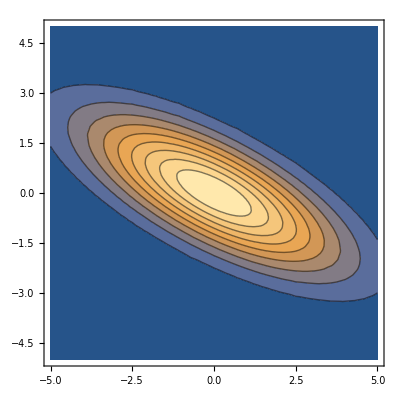

```mathematica
ContourPlot[g[x,y,2,1,20*π/180],{x,-5,5},{y,-5,5}]
```

```mathematica
c={{c11,c12},{c21,c22}}
```

{{c11,c12},{c21,c22}}

```mathematica
ic=Inverse[c]
```

{{c22/(-c12 c21+c11 c22),-c12/(-c12 c21+c11 c22)},{-c21/(-c12 c21+c11 c22),c11/(-c12 c21+c11 c22)}}

```mathematica
eq1=ic[[1]][[1]]==Cos[a]^2/(2 sx^2)+Sin[a]^2/(2 sy^2)
eq2=ic[[2]][[2]]==Sin[a]^2/(2 sx^2)+Cos[a]^2/(2 sy^2)
eq3=ic[[1]][[2]]==Sin[a]Cos[a]/sy^2
eq4=ic[[2]][[1]]==Sin[a]Cos[a]/sx^2
```

c22/(-c12 c21+c11 c22)==Cos[a]^2/(2 sx^2)+Sin[a]^2/(2 sy^2)

c11/(-c12 c21+c11 c22)==Cos[a]^2/(2 sy^2)+Sin[a]^2/(2 sx^2)

-c12/(-c12 c21+c11 c22)==(Cos[a] Sin[a])/sy^2

-c21/(-c12 c21+c11 c22)==(Cos[a] Sin[a])/sx^2

```mathematica
Solve[{eq1,eq2,eq3},{a,sx,sy}]//Simplify
```

$Aborted

```mathematica
c={{Cos[a]^2/(2 sx^2)+Sin[a]^2/(2 sy^2),Sin[a]Cos[a]/sy^2},
{Sin[a]Cos[a]/sx^2,Sin[a]^2/(2 sx^2)+Cos[a]^2/(2 sy^2)}}
```

{{Cos[a]^2/(2 sx^2)+Sin[a]^2/(2 sy^2),(Cos[a] Sin[a])/sy^2},{(Cos[a] Sin[a])/sx^2,Cos[a]^2/(2 sy^2)+Sin[a]^2/(2 sx^2)}}

```mathematica
Inverse[c]//FullSimplify
```

{{(16 sx^2 sy^2 (sx^2 Cos[a]^2+sy^2 Sin[a]^2))/((sx^2+sy^2)^2-(sx^4-6 sx^2 sy^2+sy^4) Cos[4 a]),-(32 sx^4 sy^2 Cos[a] Sin[a])/((sx^2+sy^2)^2-(sx^4-6 sx^2 sy^2+sy^4) Cos[4 a])},{-(32 sx^2 sy^4 Cos[a] Sin[a])/((sx^2+sy^2)^2-(sx^4-6 sx^2 sy^2+sy^4) Cos[4 a]),(16 sx^2 sy^2 (sy^2 Cos[a]^2+sx^2 Sin[a]^2))/((sx^2+sy^2)^2-(sx^4-6 sx^2 sy^2+sy^4) Cos[4 a])}}

```mathematica
eq1=sx2==a2 Cos[θ]^2+b2 Sin[θ]^2
eq2=sy2==a2 Sin[θ]^2+b2 Cos[θ]^2
Solve[{eq1,eq2},{a2,b2}]//FullSimplify
```

sx2==a2 Cos[θ]^2+b2 Sin[θ]^2

sy2==b2 Cos[θ]^2+a2 Sin[θ]^2

{{a2→1/2 (sx2+sy2+(sx2-sy2) Sec[2 θ]),b2→1/2 (sx2+sy2+(-sx2+sy2) Sec[2 θ])}}

```mathematica
g[x_,y_,s_]:=Exp[-x^2/(2 s^2)-y^2/(2 s^2)]
```

```mathematica
Integrate[g[x,y,s],{y,0,1},Assumptions->s>0]/Integrate[g[x,y,s],{y,0,∞},Assumptions->s>0]/.s->1//N
```

0.682689

```mathematica
f[x_]:=Exp[-x^2/2]
```

```mathematica
c1=Integrate[f[x],{x,0,1}]/Integrate[f[x],{x,0,∞}]
```

Erf[1/(√2)]

```mathematica
Integrate[f[r]r,{r,0,1}]/Integrate[f[r]r,{r,0,∞}]
```

1-1/(√ⅇ)

```mathematica
Solve[Integrate[f[r]r,{r,0,x}]/Integrate[f[r]r,{r,0,∞}]==Erf[1/(√2)],x]
```

{{x→ConditionalExpression[-√2 √(2 ⅈ π C[1]-Log[1-Erf[1/(√2)]]),C[1]∈Integers]},{x→ConditionalExpression[√2 √(2 ⅈ π C[1]-Log[1-Erf[1/(√2)]]),C[1]∈Integers]}}

```mathematica
c1=√2 √(-Log[1-Erf[1/(√2)]])//FullSimplify
```

```mathematica
√(-2 Log[Erfc[2/(√2)]])//N
```

2.48598

```mathematica
c1//N
```

1.51517

```mathematica
Erf[1/Sqrt[2]]//N
```

0.682689

```mathematica
f[1]//N
```

0.606531

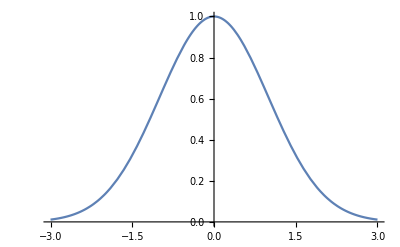

```mathematica
Plot[f[x],{x,-3,3}]
```

## Calculation of Fisher matrix for gauss2d model

```mathematica
X2=(di-fi)^2/yerr^2/.fi->Exp[-(x-x0)^2/2-(y-y0)^2/2];
```

```mathematica
D[X2,{x0,2}]
```

1/yerr^2(2 ⅇ^(-1/2 (x-x0)^2-1/2 (y-y0)^2) (di-ⅇ^(-1/2 (x-x0)^2-1/2 (y-y0)^2))+2 ⅇ^(-(x-x0)^2-(y-y0)^2) (x-x0)^2-2 ⅇ^(-1/2 (x-x0)^2-1/2 (y-y0)^2) (di-ⅇ^(-1/2 (x-x0)^2-1/2 (y-y0)^2)) (x-x0)^2)

```mathematica
D[X2,{y0,2}]
```

1/yerr^2(2 ⅇ^(-1/2 (x-x0)^2-1/2 (y-y0)^2) (di-ⅇ^(-1/2 (x-x0)^2-1/2 (y-y0)^2))+2 ⅇ^(-(x-x0)^2-(y-y0)^2) (y-y0)^2-2 ⅇ^(-1/2 (x-x0)^2-1/2 (y-y0)^2) (di-ⅇ^(-1/2 (x-x0)^2-1/2 (y-y0)^2)) (y-y0)^2)

```mathematica
D[D[X2,x0],y0]
```

(2 ⅇ^(-(x-x0)^2-(y-y0)^2) (x-x0) (y-y0))/yerr^2-(2 ⅇ^(-1/2 (x-x0)^2-1/2 (y-y0)^2) (di-ⅇ^(-1/2 (x-x0)^2-1/2 (y-y0)^2)) (x-x0) (y-y0))/yerr^2

## y = a*x^2 + b

```mathematica
X2=(di-fi)^2/yerr^2/.fi->a*x^2+b
D[X2,{a,2}]
D[X2,{b,2}]
D[D[X2,a],b]
```

((-b+di-a x^2)^2)/yerr^2

(2 x^4)/yerr^2

2/yerr^2

(2 x^2)/yerr^2